I picked 4 different Matrix Market 
They were supposed to be symmetric Indefinite Matrices but they are not! 
I built some linear inequality constraints  and exported the inequality matrices as suitable files.

## BFW62B

https://math.nist.gov/MatrixMarket/data/NEP/bfwave/bfw62b.html

This matrix has all negative eigenvalues!  I am going to flip the matrix and make a few dense constraint rows.

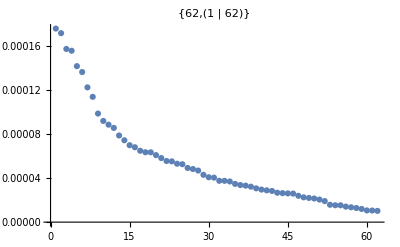

```mathematica
A=-Import["https://math.nist.gov/pub/MatrixMarket2/NEP/bfwave/bfw62b.mtx.gz"];
m=Length[A];λs=Eigenvalues[A];
ListPlot[λs,
PlotRange->All,
PlotLabel->{m,Tally[Sign[λs]]}
]
```

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\MA5630\\Project Code"]
g=ConstantArray[1,m];
g=RandomReal[{-1,1},m];
c=9;
B=RandomReal[{-1,1},{c,m}];
b=ConstantArray[1,c];
cons=Table[B⟦i⟧.vars-b⟦i⟧>0,{i,c}];
Clear[x]
vars=Array[x,m];
{min,sub}=FindMinimum[{0.5 vars.A.vars+g.vars,cons}, {vars,RandomReal[{-1,1},m]}ᵀ];
xMin=vars/.sub;
Export["A62.mtx",A];
Export["B62.tsv",B];
Export["xMin62.tsv",xMin];
{min,cons⟦All,1⟧/.sub}
```

C:\Users\struther\Desktop\2022-23-Classes\MA5630\Project Code

Dot::dotsh: Tensors {0.355543,0.247069,0.684087,-0.825156,0.724564,-0.331875,-0.591803,-0.920874,0.183072,-0.403403,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

Dot::dotsh: Tensors {0.580042,-0.945205,-0.532063,-0.536976,0.0378259,0.837777,-0.411256,-0.536664,-0.718708,0.491011,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {0.355543,0.247069,0.684087,-0.825156,0.724564,-0.331875,-0.591803,-0.920874,0.183072,-0.403403,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

Dot::dotsh: Tensors {0.580042,-0.945205,-0.532063,-0.536976,0.0378259,0.837777,-0.411256,-0.536664,-0.718708,0.491011,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

Dot::dotsh: Tensors {0.276373,0.0437367,0.320297,-0.903033,0.603403,-0.877478,0.724022,-0.789459,-0.475207,0.757159,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Set::shape: Lists {min,sub} and FindMinimum[{0.5 vars.A.vars+g.vars,cons},Transpose[{vars,RandomReal[{-1,1},m]}]] are not the same shape.

Dot::dotsh: Tensors {0.355543,0.247069,0.684087,-0.825156,0.724564,-0.331875,-0.591803,-0.920874,0.183072,-0.403403,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

Dot::dotsh: Tensors {0.580042,-0.945205,-0.532063,-0.536976,0.0378259,0.837777,-0.411256,-0.536664,-0.718708,0.491011,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

Dot::dotsh: Tensors {0.276373,0.0437367,0.320297,-0.903033,0.603403,-0.877478,0.724022,-0.789459,-0.475207,0.757159,«52»} and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«484»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{-0.656476,{-1+{0.355543,0.247069,0.684087,-0.825156,0.724564,-0.331875,-0.591803,-0.920874,0.183072,-0.403403,0.162016,-0.821529,-0.126031,-0.327891,-0.190468,0.262009,0.702512,0.944687,0.526515,-0.031792,0.867811,0.275887,0.505448,0.551856,0.516762,-0.769525,0.625408,0.0466225,0.922185,-0.338122,-0.636011,0.373293,-0.0134582,-0.945488,0.0118716,-0.846409,0.696065,0.47744,-0.195554,-0.566176,-0.044838,-0.257454,0.818843,-0.0264033,0.529256,-0.484979,-0.573239,-0.932574,-0.658698,-0.805357,-0.0429465,-0.330102,-0.123414,0.748663,-0.252081,0.00731873,-0.409829,0.656401,-0.849298,-0.457897,0.127811,0.986971}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{0.580042,-0.945205,-0.532063,-0.536976,0.0378259,0.837777,-0.411256,-0.536664,-0.718708,0.491011,0.525841,-0.452019,0.267677,-0.249669,-0.89729,0.691915,-0.570082,-0.424037,0.240303,-0.974522,0.990864,0.612302,-0.857863,-0.318266,-0.3593,0.613789,0.281936,-0.640615,-0.359163,-0.904063,0.214435,-0.998063,-0.0944014,-0.794964,-0.843833,-0.887958,0.72512,0.251316,0.667526,0.921901,-0.955312,0.745669,0.0882325,-0.710367,0.0527496,-0.18593,0.742406,-0.343024,-0.357019,-0.788216,0.795253,-0.999554,0.5445,-0.863952,0.438832,-0.660894,0.0676512,-0.668042,-0.643171,-0.687939,0.569084,-0.446361}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{0.276373,0.0437367,0.320297,-0.903033,0.603403,-0.877478,0.724022,-0.789459,-0.475207,0.757159,0.866603,0.306058,-0.749544,-0.680495,-0.0386026,-0.429118,-0.711004,0.752738,0.0758006,0.64694,-0.4058,-0.795112,0.460591,-0.506652,-0.0304601,-0.841234,-0.76909,0.0674361,0.150308,-0.28488,-0.333304,-0.291876,-0.413241,0.0918252,0.794548,-0.332906,0.474986,-0.63669,0.35089,-0.786652,-0.37267,-0.313948,-0.240448,-0.828332,-0.289722,0.231893,-0.866491,-0.147498,0.341895,0.244706,0.830195,-0.669238,0.576395,-0.94441,-0.155126,-0.627719,0.371029,0.212308,0.916477,-0.672189,0.555203,0.0661833}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{-0.74818,0.866169,-0.987778,-0.520912,0.827752,0.81103,-0.236506,-0.627282,0.798106,0.760864,0.621824,-0.253411,-0.778389,-0.535998,-0.234945,0.209884,0.632012,0.922686,0.612999,0.379331,-0.424736,0.501376,-0.720877,-0.46859,0.274023,0.923232,-0.947436,0.717977,0.818509,0.709713,-0.885176,0.681653,-0.265279,-0.316014,0.974048,-0.129845,-0.831797,0.715553,0.789025,-0.486274,0.924396,-0.243628,-0.183567,-0.458384,-0.817162,-0.0165426,-0.184143,-0.479016,-0.276727,0.205101,-0.102076,0.831096,0.90823,0.48704,-0.507785,-0.0400737,0.485274,0.179101,0.288889,0.800691,0.765118,-0.991407}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{-0.884739,0.595972,0.473089,-0.78636,-0.62929,0.651482,-0.437626,0.273888,0.483885,0.432376,-0.800073,0.474845,0.612485,-0.324843,-0.0104086,-0.808238,-0.627761,0.606937,-0.676539,-0.890459,0.925333,0.209012,-0.299025,0.238943,-0.892294,-0.457791,0.0581636,-0.958401,0.709283,-0.814283,-0.834252,-0.76205,0.412141,-0.0429376,-0.823081,-0.601581,-0.435844,0.0367485,0.0330197,-0.723107,0.904937,0.313673,0.937699,-0.909417,0.34568,0.207967,0.406422,0.28447,0.825111,0.469133,0.38337,-0.597381,-0.800117,0.393353,0.677724,-0.473714,0.631925,-0.38751,0.464021,0.652452,0.0531461,-0.243628}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{0.72554,0.880688,-0.195958,0.814667,0.986026,0.450566,-0.902727,-0.209061,-0.32192,-0.873811,-0.490178,-0.826247,-0.460834,0.819974,-0.183641,-0.724069,0.451364,-0.0648155,-0.101676,-0.0175622,-0.487824,-0.414378,0.303035,0.293315,0.897337,0.466192,0.671915,0.411842,0.489087,0.719064,0.555477,-0.786915,0.821803,-0.93718,0.0299385,0.941808,0.762636,-0.34929,-0.938282,-0.164277,-0.270325,-0.459795,-0.585748,0.335569,-0.151403,-0.912666,0.451153,-0.240375,0.517033,0.645902,0.801369,0.669191,0.086023,-0.989821,-0.0325549,0.304418,0.604603,0.901324,0.231174,-0.0198604,0.344606,-0.967293}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{-0.470941,0.625087,0.135365,-0.836874,-0.800322,0.37741,-0.751599,-0.273939,-0.971183,-0.278076,0.315378,-0.874874,-0.296536,0.902184,-0.726112,-0.696089,0.511434,-0.25812,0.926746,0.368216,-0.191109,-0.824758,0.425158,0.0630117,-0.0104575,-0.649179,0.415861,0.0315757,0.414063,-0.176641,0.979131,0.952144,0.805582,0.668264,-0.896986,0.129151,0.286864,0.771509,0.500445,-0.828902,0.961421,-0.0539497,0.859617,0.542043,-0.599078,0.463813,-0.938901,0.211358,-0.0223679,-0.739778,0.778525,0.808752,0.609193,0.949432,0.778225,-0.526467,-0.157668,-0.145595,-0.152518,-0.374404,0.770175,-0.703078}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{0.384856,-0.323957,0.473538,-0.451815,0.347187,-0.826912,0.296584,-0.374585,0.745669,-0.43706,0.696183,0.686218,-0.34505,0.945756,0.405656,-0.0780811,0.198095,0.433366,-0.676993,-0.301263,-0.456036,0.310082,-0.64293,0.712499,0.97407,0.468722,0.781027,-0.938252,-0.330794,-0.755062,0.267697,-0.95244,0.378629,-0.0236249,0.590656,0.944962,-0.642836,0.060196,-0.0691305,-0.546167,0.923304,-0.0875905,-0.741521,-0.256315,0.0101019,0.743008,-0.0439807,0.0875086,0.840432,-0.628214,0.254777,0.28878,0.192596,0.558171,0.83443,0.105369,-0.840752,-0.206416,-0.89224,0.00162237,-0.377338,-0.678082}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417},-1+{0.552591,-0.7778,-0.73249,0.483764,-0.157142,0.969691,-0.48696,0.254798,-0.505955,-0.44174,-0.496157,-0.439799,-0.809045,-0.12958,0.455858,-0.67011,-0.389329,-0.572992,0.43913,-0.470607,0.954995,0.365899,-0.63654,0.195524,0.497678,0.911699,-0.4698,-0.92899,0.636925,0.471865,0.364968,0.816448,0.1777,0.892231,-0.659189,-0.311659,-0.918923,-0.7168,0.9345,-0.988612,0.893511,-0.219197,-0.384306,-0.721027,0.307585,-0.81474,-0.434437,-0.446512,-0.835632,-0.562369,0.156254,0.582266,-0.362498,-0.806198,-0.622017,0.222815,0.917799,0.710954,-0.316841,-0.837753,-0.405183,0.966589}.{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628,0.0928541,0.0297895,-0.0552693,-0.049992,-0.0406901,-0.158572,0.0112351,0.0157817,0.142654,0.342856,0.177543,0.229324,0.0084697,0.0217481,0.0894567,-0.0208175,-0.0020394,0.127982,0.128101,0.0742246,0.15532,0.109947,2.18935,-0.0533292,-0.0266509,-0.0984631,0.133376,-0.670109,-0.0971649,-0.473804,-0.452756,0.617728,0.533199,0.547326,0.282226,0.319983,0.37352,0.355805,0.120386,0.441761,0.587483,0.321792,0.298935,0.147719,0.0917073,0.0365245,0.00396613,0.414692,0.438602,-0.340866,-2.84341,0.286406,-0.166434,-0.364958,-0.431066,-0.513452,-0.00608017,-0.203957,-0.0517808,-0.0956508,0.418251,-0.0867625,-0.136865,0.240536,0.186908,0.0757015,0.0765376,-0.0137403,0.0639391,-0.0385889,-0.153411,-0.326627,-0.169622,-0.11746,-0.257051,0.216745,-0.809653,0.0842774,0.0963692,-0.0684378,0.124855,0.0778727,0.244998,0.256146,-0.0413784,0.0655766,0.128586,0.139474,1.18752,1.15552,0.0409593,0.0705886,-0.0832687,0.273511,0.283671,0.23561,0.252292,0.100465,0.0956626,0.235171,0.63088,0.280801,-0.0672178,0.05503,-0.685569,-0.669997,0.0713132,-0.0294543,0.149968,0.124908,0.110495,0.110549,0.110522,0.220896,-0.857557,-0.652484,-1.22717,-1.16451,-0.11966,0.0565515,0.0575606,0.0449,0.0601206,0.115259,-0.164167,0.433277,0.418893,-0.172922,-0.0471591,0.34873,0.186915,0.134468,0.0789848,0.0808852,0.0858526,0.0700323,-0.0423424,-0.198189,0.0830206,0.0482456,0.0355114,0.122915,0.0461342,0.146153,0.0804953,0.0957298,0.301902,0.274649,0.0984802,0.0839872,0.289279,0.313842,0.310705,0.416708,0.259019,0.292329,0.00578243,0.503707,0.190004,0.506583,1.05541,0.102336,0.0776274,0.0768891,0.0219404,0.0779388,0.0981604,0.0767429,0.454826,0.111575,0.0619146,0.0769497,0.0669945,0.0908633,0.131579,0.0435038,0.041377,0.0755763,0.0749848,0.0774361,0.076291,0.0350352,-0.0598654,0.327217,0.278001,0.577068,0.609377,0.626054,0.629956,0.39443,-0.10759,-0.0071787,-0.0270075,1.41782,0.140781,0.0221568,0.883866,-0.127339,-0.210836,-0.877381,0.00318505,0.407505,-0.699023,-0.206035,-0.205623,-0.251603,-0.0582071,0.0686466,0.0343775,-0.221725,0.706796,-0.0569916,0.126428,-0.0479085,-0.0315997,0.703646,0.187391,-1.28499,0.104842,0.212149,-0.0534108,0.171542,0.0961456,0.367621,0.150225,0.418844,0.217985,-0.540454,0.139284,0.0714135,0.0841643,0.00350844,0.039822,0.136329,0.106249,-0.13516,0.0429619,-0.0393048,0.0385759,-0.189528,-0.102772,-0.189872,-0.0784792,-0.516118,-0.0739175,-0.51082,-1.2753,-0.0953944,-0.604097,0.274019,0.633868,-0.787923,0.0746,0.101752,0.0960807,-0.165821,-0.0318847,-0.135095,0.371772,-0.037355,0.105923,-0.368497,-0.0143022,-0.0822087,-0.0317402,0.111766,-0.186197,-0.141715,-0.114537,-0.130181,0.0652931,1.88088,0.337035,0.333057,0.0811026,-0.100285,-0.0138906,-0.163305,-0.0805817,1.78894,0.343321,1.07392,0.337977,0.311369,-0.604197,1.18522,0.11769,0.208327,-0.123416,0.120438,0.0656642,0.0428549,0.0554085,0.0918169,0.820519,0.522748,0.278099,0.26738,0.606115,0.211665,-0.36753,-0.619031,-0.400552,-0.301651,0.235041,-0.434295,0.0497408,0.125012,0.0374981,0.188202,0.0804593,0.188058,0.437756,-0.204162,0.101129,0.109748,0.121205,0.176776,-0.116191,0.176834,-0.317992,0.0706263,-0.406171,-0.324487,0.267226,0.16619,-0.131925,0.0784199,0.0958246,-0.107147,-0.046078,-0.140542,-0.152015,-0.11997,-0.0631643,-0.0923488,-0.0890923,-0.0714292,-0.0332853,-0.0620565,0.0513491,0.0784933,0.0942781,0.0995848,0.0995234,0.101051,0.125076,0.0982411,-0.0643792,0.0648843,0.0775869,0.0575653,0.05958,0.0339471,0.0751125,0.075417}}}

## BCSTK22

https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc3/bcsstk22.html

This matrix has all positive eigenvalues!  I am going to make a few dense constraint rows.

Eigenvalues::arh: Because finding 138 out of the 138 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

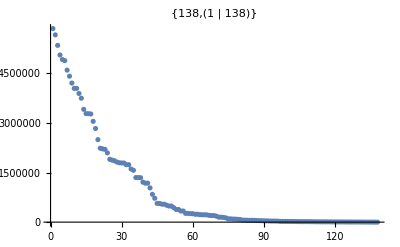

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc3/bcsstk22.mtx.gz"];
m=Length[A];λs=Eigenvalues[A];
ListPlot[λs,
PlotRange->All,
PlotLabel->{m,Tally[Sign[λs]]}
]
```

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\MA5630\\Project Code"]
g=ConstantArray[1,m];
g=RandomReal[{-1,1},m];
c=12;
nnz=3m;
B=SparseArray[Band[{1,1}]->1.0,{c,m}];
Do[
i=RandomInteger[{1,c}];
j=RandomInteger[{1,m}];
 B⟦i,j⟧+=RandomReal[{-1,1}],{nnz}]
b=ConstantArray[1,c];
cons=Table[B⟦i⟧.vars-b⟦i⟧>0,{i,c}];
Clear[x]
vars=Array[x,m];
{min,sub}=FindMinimum[{0.5 vars.A.vars+g.vars,cons}, {vars,RandomReal[{-1,1},m]}ᵀ];
xMin=vars/.sub;
Export["A138.mtx",A];
Export["B138.mtx",B];
Export["xMin138.tsv",xMin];
{min,cons⟦All,1⟧/.sub}
```

C:\Users\struther\Desktop\2022-23-Classes\MA5630\Project Code

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,26},{{1},«24»,{46}}},{1.,-0.353976,-0.161264,-0.27139,-0.311753,-0.512991,-0.28927,-0.412586,0.373688,0.875312,«16»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,38},{{2},«36»,{131}}},{1.,-0.122386,0.414879,0.748384,0.356285,0.896874,-0.0956913,-0.0184839,0.0766257,-0.727944,«28»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,28},{«1»}},{1.93395,-0.472607,-0.658918,0.915866,0.502521,0.766987,-0.616542,-0.77187,-0.315301,-0.910238,«18»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,26},{{1},«24»,{46}}},{1.,-0.353976,-0.161264,-0.27139,-0.311753,-0.512991,-0.28927,-0.412586,0.373688,0.875312,«16»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,38},{{2},«36»,{131}}},{1.,-0.122386,0.414879,0.748384,0.356285,0.896874,-0.0956913,-0.0184839,0.0766257,-0.727944,«28»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,28},{«1»}},{1.93395,-0.472607,-0.658918,0.915866,0.502521,0.766987,-0.616542,-0.77187,-0.315301,-0.910238,«18»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Set::shape: Lists {min,sub} and FindMinimum[{0.5 vars.A.vars+g.vars,cons},Transpose[{vars,RandomReal[{-1,1},m]}]] are not the same shape.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,26},{{1},«24»,{46}}},{1.,-0.353976,-0.161264,-0.27139,-0.311753,-0.512991,-0.28927,-0.412586,0.373688,0.875312,«16»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,38},{{2},«36»,{131}}},{1.,-0.122386,0.414879,0.748384,0.356285,0.896874,-0.0956913,-0.0184839,0.0766257,-0.727944,«28»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,28},{«1»}},{1.93395,-0.472607,-0.658918,0.915866,0.502521,0.766987,-0.616542,-0.77187,-0.315301,-0.910238,«18»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«52»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{-0.656476,{-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403}}}

## Plat362

https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/platz/plat362.html

This matrix has all positive eigenvalues!  I am going to make a few dense constraint rows.

Eigenvalues::arh: Because finding 362 out of the 362 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

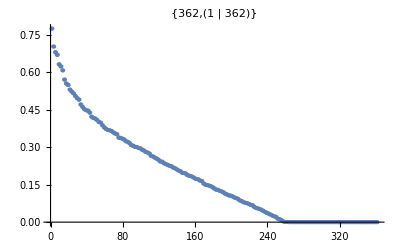

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/platz/plat362.mtx.gz"];
m=Length[A];λs=Eigenvalues[A];
ListPlot[λs,
PlotRange->All,
PlotLabel->{m,Tally[Sign[λs]]}
]
```

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\MA5630\\Project Code"]
g=ConstantArray[1,m];
g=RandomReal[{-1,1},m];
c=43;
nnz=3m;
B=SparseArray[Band[{1,1}]->1.0,{c,m}];
Do[
i=RandomInteger[{1,c}];
j=RandomInteger[{1,m}];
 B⟦i,j⟧+=RandomReal[{-1,1}],{nnz}]
b=ConstantArray[1,c];
cons=Table[B⟦i⟧.vars-b⟦i⟧>0,{i,c}];
Clear[x]
vars=Array[x,m];
{min,sub}=FindMinimum[{0.5 vars.A.vars+g.vars,cons}, {vars,RandomReal[{-1,1},m]}ᵀ];
xMin=vars/.sub;
Export["A362.mtx",A];
Export["B362.mtx",B];
Export["xMin362.tsv",xMin];
{min,cons⟦All,1⟧/.sub}
```

C:\Users\struther\Desktop\2022-23-Classes\MA5630\Project Code

Dot::dotsh: Tensors «1» and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,28},{{2},«26»,{185}}},{1.,0.280212,-0.431677,0.562942,-0.145141,-0.367805,0.0799763,0.0287224,-0.976173,0.6391,«18»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,{362},0,{1,{{0,26},{{3},«24»,{4}}},{1.,-0.482517,0.36241,0.770024,-0.933828,0.99702,0.585517,-0.139364,0.83126,-0.692254,«16»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors «1» and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,28},{{2},«26»,{185}}},{1.,0.280212,-0.431677,0.562942,-0.145141,-0.367805,0.0799763,0.0287224,-0.976173,0.6391,«18»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,{362},0,{1,{{0,26},{{3},«24»,{4}}},{1.,-0.482517,0.36241,0.770024,-0.933828,0.99702,0.585517,-0.139364,0.83126,-0.692254,«16»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Set::shape: Lists {min,sub} and FindMinimum[{0.5 vars.A.vars+g.vars,cons},Transpose[{vars,RandomReal[{-1,1},m]}]] are not the same shape.

Dot::dotsh: Tensors «1» and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,28},{{2},«26»,{185}}},{1.,0.280212,-0.431677,0.562942,-0.145141,-0.367805,0.0799763,0.0287224,-0.976173,0.6391,«18»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,{362},0,{1,{{0,26},{{3},«24»,{4}}},{1.,-0.482517,0.36241,0.770024,-0.933828,0.99702,0.585517,-0.139364,0.83126,-0.692254,«16»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«128»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{-0.656476,{-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628},-1+SparseArray[…].{-0.000535561,0.150884,0.551458,0.0722218,0.183024,0.789894,0.179271,0.0538005,0.318938,0.0824064,0.30568,0.276635,-0.161864,0.755856,0.403611,0.186834,0.0724783,-0.0416583,0.320963,0.0631722,0.00614748,0.039538,0.012317,0.84655,0.640035,0.0971191,0.284381,0.282524,0.391327,0.184381,0.109432,-0.439558,0.650081,0.659888,0.276261,0.607274,0.116338,-0.0607824,-0.00803,-0.0563747,0.393843,0.577349,0.411442,0.302454,0.313143,-0.409488,0.284401,0.0792005,0.190826,0.204811,0.0922335,0.535388,0.083084,-0.148397,0.159976,0.0788995,0.385953,-0.0513052,0.00700948,-0.0864871,1.53932,0.368403,0.262648,1.34568,0.282397,0.287506,-0.00829381,0.0776971,0.0257557,-0.00717529,-0.0255918,-0.0560635,0.0311819,0.0467654,-0.057042,-0.0316533,0.45346,0.513678,0.274759,0.157779,-0.118609,0.0900205,-0.640139,0.484496,0.162435,0.0448138,0.165478,0.159827,0.573809,-0.0873755,-0.0762816,-0.228797,-0.088668,-0.119186,-0.201978,-0.22085,0.549537,0.106431,0.0808222,0.075977,0.407065,0.409946,0.0901234,-0.177644,-0.453322,-1.19258,-0.010335,-0.175619,0.244325,0.13168,0.747103,0.458931,-0.180709,0.252677,0.354147,0.244325,0.22646,0.0396135,0.189774,0.0682832,0.560515,0.37582,0.494597,0.0463261,-0.929405,-1.2176,0.174959,0.18792,0.150815,-0.0651246,-0.0320221,-0.0711937,-0.0515919,-0.0674204,0.0493027,-0.0574373,-0.0501829,0.408628}}}

## 494Bus

https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/psadmit/494_bus.html

This matrix has all positive eigenvalues!  I am going to make a few dense constraint rows.

Eigenvalues::arh: Because finding 494 out of the 494 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

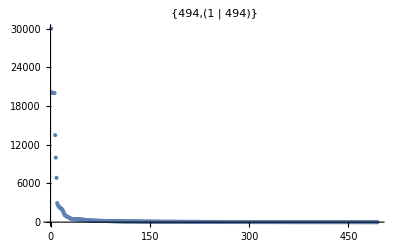

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/psadmit/494_bus.mtx.gz"];
m=Length[A];λs=Eigenvalues[A];
ListPlot[λs,
PlotRange->All,
PlotLabel->{m,Tally[Sign[λs]]}
]
```

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\MA5630\\Project Code"]
g=ConstantArray[1,m];
g=RandomReal[{-1,1},m];
c=43;
nnz=3m;
B=SparseArray[Band[{1,1}]->1.0,{c,m}];
Do[
i=RandomInteger[{1,c}];
j=RandomInteger[{1,m}];
 B⟦i,j⟧+=RandomReal[{-1,1}],{nnz}]
b=ConstantArray[1,c];
cons=Table[B⟦i⟧.vars-b⟦i⟧>0,{i,c}];
Clear[x]
vars=Array[x,m];
{min,sub}=FindMinimum[{0.5 vars.A.vars+g.vars,cons}, {vars,RandomReal[{-1,1},m]}ᵀ];
xMin=vars/.sub;
Export["A494.mtx",A];
Export["B494.mtx",B];
Export["xMin494.tsv",xMin];
{min,cons⟦All,1⟧/.sub}
```

C:\Users\struther\Desktop\2022-23-Classes\MA5630\Project Code

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,33},{{1},«31»,{347}}},{1.,0.452815,0.650564,-0.859283,0.567932,-0.482456,0.00155345,-0.973386,0.677004,-0.421428,«23»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

Dot::dotsh: Tensors «1» and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,{494},0,{1,{{0,42},{{3},«40»,{294}}},{1.,-0.73422,0.0621528,-0.55687,0.387468,0.846314,0.684306,0.288615,0.859408,-0.96025,«32»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,33},{{1},«31»,{347}}},{1.,0.452815,0.650564,-0.859283,0.567932,-0.482456,0.00155345,-0.973386,0.677004,-0.421428,«23»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

Dot::dotsh: Tensors «1» and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,{494},0,{1,{{0,42},{{3},«40»,{294}}},{1.,-0.73422,0.0621528,-0.55687,0.387468,0.846314,0.684306,0.288615,0.859408,-0.96025,«32»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Set::shape: Lists {min,sub} and FindMinimum[{0.5 vars.A.vars+g.vars,cons},Transpose[{vars,RandomReal[{-1,1},m]}]] are not the same shape.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,33},{{1},«31»,{347}}},{1.,0.452815,0.650564,-0.859283,0.567932,-0.482456,0.00155345,-0.973386,0.677004,-0.421428,«23»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

Dot::dotsh: Tensors «1» and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

Dot::dotsh: Tensors SparseArray[Automatic,{494},0,{1,{{0,42},{{3},«40»,{294}}},{1.,-0.73422,0.0621528,-0.55687,0.387468,0.846314,0.684306,0.288615,0.859408,-0.96025,«32»}}] and {x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],«352»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{-0.656476,{-1+SparseArray[…].{-0.000535561,0.150884,0.551458,356,0.171542,0.0961456,0.367621},41,-1+SparseArray[…].{1}}}
 |  |  |  |